# Camera Calibration Using Accelerometer and Horizon Line

## Okay Arık and Seniha Esen Yuksel, Senior Member, IEEE

## Hacettepe University, Department of Electrical and Electronics Engineering, 06800, Beytepe, Ankara, Turkey

## okayarik@hacettepe.edu.tr, eyuksel@ee.hacettepe.edu.tr

## Calibration Application

The calibration application can be installed on an Android device using CamAcc.apk file. The application captures images and records the acceleration data synchronously. Take around 20 photos of the horizon line by roughly rotating the device one turn around the principal axis of the camera. Images are saved inside CamAcc folder. Recorded acceleration data and corresponding image names are saved in acc.dat file in the same folder.

## Accelation Vectors

Computation of the bias of the accelerometer using records with 6 orientations (top, bottom, right, left, up, down) in abs.dat file

```mathematica
abs=Total[Partition[Map[#*UnitStep[Abs[#]-5000]&,Flatten[Take[Import[NotebookDirectory[]<>"abs.dat"],All,{2,4}]]],3]]/2.;
```

Import the accelerometer data, subtract the bias and normalize

```mathematica
acc=Take[Import[NotebookDirectory[]<>"H\\acc.dat"],All,{2,4}];
acv=Map[Normalize[#-abs]&,acc];
```

Number of images

```mathematica
is=Dimensions[acv][[1]];
```

## Detection of the Horizon Line

List of the images

```mathematica
fls=Select[Import[NotebookDirectory[]<>"H"],StringContainsQ[#,"IMG"]&];
```

Number of images

```mathematica
is=Dimensions[fls][[1]];
```

Null matrix for vanishing points

```mathematica
hr=Table[0,{is},{4}];
```

Index of the image

```mathematica
in=1; (*in=1,2,...,is*)
```

Import the image

```mathematica
im=Import[NotebookDirectory[]<>"H\\"<>fls[[in]]];
```

Line detection using Hough method

```mathematica
ln=ImageLines[EdgeDetect[im,10]];
```

Select the horizontal lines using acceleration vector

```mathematica
hri=Select[ln,Abs[Normalize[{1,-1}.#].({{0, -1}, {1, 0}}).Normalize[(Take[#,2]/N[#[[3]]])&[acv[[in]]]]]<.1&];
```

Visualize the selected horizontal lines

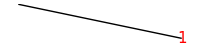

```mathematica
Graphics[{Map[Line,hri],
Table[Text[Style[n,15,Red],vt[[n,2]]],{n,1,Dimensions[hri][[1]]}]},ImageSize->200]
```

Drop the outlier lines, if any.

```mathematica
hri=Drop[hri,{6}];
```

Append the horizontal line to the list

```mathematica
hr[[in]]=hri;
```

Save the computed horizontal lines

```mathematica
If[Count[hr,0,2]==0,Export[NotebookDirectory[]<>"H\\hr.dat",hr]];
```

## Estimation of Projection Matrix

Inverse transpose of camera matrix K^-T maps the unbiased a_n acceleration vectors to λ_n horizon lines (λ_n^T h̃=0): λ_n~K^-T a_n

Import the horizontal lines computed above

```mathematica
hr=Import[NotebookDirectory[]<>"H\\hr.dat"];
```

Transform the computed vanishing points to the coordinate system having the origin at the left-top corner.

```mathematica
hr=Partition[Map[{3456-#[[2]],#[[1]]}&,Partition[Flatten[hr],2]],2];
```

Copmpute λ_n normal vectors which determine the horizontal line (λ_n^T h̃=0) passing through h_1 and h_2.

```mathematica
nr=Map[-Inverse[#].{1,1}&,hr];
```

Get the spherical projection function (SP1) and its Jacobian (JSP1).

```mathematica
Get[NotebookDirectory[]<>"functions.wl"]
```

Reorganize the vectors

```mathematica
acv=Map[Reverse,acv];
nr=Map[Take[#,2]/#[[3]]&,Map[Reverse[Flatten[{#,1}]]&,nr]];
```

Optimization of the projection error function in Eq. 7 using Newton’s method for Model 3: P~K

Initialize:

```mathematica
k1 = 1/3000.; k2 = 2300.*k1; k3 = 1700.*k1; k4 = 3000.*k1; k5 =0.;
```

Iterate:

```mathematica
For[n=1,n≤10,n=n+1,
dk=-PseudoInverse[Flatten[Table[JSP1[k1,k2,k3,k4,k5,nr[[n,1]],nr[[n,2]]],{n,is}],1]].Flatten[Table[
If[SP1[k1,k2,k3,k4,k5,nr[[n,1]],nr[[n,2]]].acv[[n]]>0,
SP1[k1,k2,k3,k4,k5,nr[[n,1]],nr[[n,2]]]-acv[[n]],SP1[k1,k2,k3,k4,k5,nr[[n,1]],nr[[n,2]]]+acv[[n]]],{n,is}],1];
{k1,k2,k3,k4,k5}={k1,k2,k3,k4,k5}+dk;
]
```

Estimated Parameters:

```mathematica
Grid[{{"Focal Length",SpanFromLeft,"Principal Point",SpanFromLeft},{"horizontal","vertical","horizontal","vertical"},{k4/k1,1/k1,k2/k1,k3/k1}},Frame->All]
```

Focal Length |  | Principal Point | 
horizontal | vertical | horizontal | vertical
3654.56 | 3628.8 | 2312.16 | 1743.75